# Laboratory 3 : GM Tubes and Counting Statistics

J.R. Powers - Luhn
02 February 2017
Thursday
Lab Partner: Tucker Jacobi

## In-lab analysis

Part A

```mathematica
PartAFilename="tjacobi_lab3_Cs137VoltageCalibration.tsv";
Plateau=Import[NotebookDirectory[]<>PartAFilename];
voltage=Table[Plateau[[i,2]],{i,12,Length[Plateau]}];
counts=Table[Plateau[[i,3]],{i,12,Length[Plateau]}];
errors=Table[√Plateau[[i,3]],{i,12,Length[Plateau]}];
PartAData=Multicolumn[Join[voltage,counts,errors],3]//First
```

{{600,0,0},{620,0,0},{640,0,0},{660,0,0},{680,0,0},{700,0,0},{720,949,√949},{740,971,√971},{760,980,14 √5},{780,1089,33},{800,1110,√1110},{820,1108,2 √277},{840,1118,√1118},{860,1158,√1158},{880,1091,√1091},{900,1159,√1159},{920,1137,√1137},{940,1170,3 √130},{960,1304,2 √326},{980,1208,2 √302},{1000,1227,√1227},{1020,1223,√1223},{1040,1161,3 √129},{1060,1250,25 √2},{1080,1288,2 √322},{1100,1306,√1306},{1120,1278,3 √142},{1140,1274,7 √26},{1160,1362,√1362},{1180,1305,3 √145},{1200,1381,√1381},{1200,1324,2 √331},{1200,1288,2 √322},{1200,1341,3 √149}}

```mathematica
Needs["ErrorBarPlots`"];
Part1DataPlot=ErrorListPlot[PartAData,Joined->False,FillingStyle->{Lighter[Orange,0.5]},FrameLabel->{Style["Voltage (V)",Black,24],Style["Counts",Black,24]},Frame->True,ImageSize->Full,PlotLabel->Style["GM Tube Counting Curve",Black,40],PlotLegends->Placed[{"Counts"},{0.25,0.85}],PlotRange->{{600,1250},{0,1500}},AxesOrigin->{600,0},FrameTicksStyle->Directive[Black,12]];
```

```mathematica
(*Trim the 0 points before we are on the counting plateau*)
PartARegressionData=PartAData[[7;;,1;;2]]
(*Now fit line to these pairs, weighted by Subscript[w, i]=1/Subscript[σ, i]*)
lmv[V_]=LinearModelFit[PartARegressionData,V,V,Weights->1/PartAData[[7;;,3]]]
```

{{720,949},{740,971},{760,980},{780,1089},{800,1110},{820,1108},{840,1118},{860,1158},{880,1091},{900,1159},{920,1137},{940,1170},{960,1304},{980,1208},{1000,1227},{1020,1223},{1040,1161},{1060,1250},{1080,1288},{1100,1306},{1120,1278},{1140,1274},{1160,1362},{1180,1305},{1200,1381},{1200,1324},{1200,1288},{1200,1341}}

FittedModel[503.725+0.704114 V]

```mathematica
A=503.72466520462103;
B=0.7041135047708155;
Part1FittedModel[V_]:=A+B*V;
numpoints=Length[PartARegressionData[[;;,1]]];
Δ=numpoints*Sum[PartARegressionData[[i,1]]^2,{i,1,numpoints}]-(Sum[PartARegressionData[[i,1]],{i,1,numpoints}])^2;
Subscript[σ, y]=√(1/(numpoints-2)*Sum[(PartARegressionData[[i,2]]-A-B*PartARegressionData[[i,1]])^2,{i,numpoints}]);
Subscript[σ, B]=√(numpoints/Δ)//N
Subscript[σ, A]=Subscript[σ, y]*√(Sum[PartARegressionData[[i,1]]^2,{i,numpoints}]/Δ)//N
```

0.00121781

53.7711

Fitting a line to these data (weighted by the standard deviation of each point) resulted in a slope of 0.7041±0.0012 counts/V and an intercept of 503.7±50 counts.

```mathematica
Part1FittedModelPlot=Plot[Part1FittedModel[V],{V,600,1250},PlotStyle->{Red,Dashed},PlotLegends->Placed[{"Linear Fit"},{0.25,0.85}],ImageSize->Full];
```

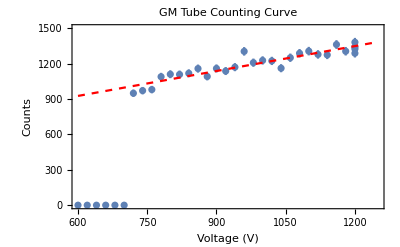

```mathematica
Show[Part1DataPlot,Part1FittedModelPlot]
```

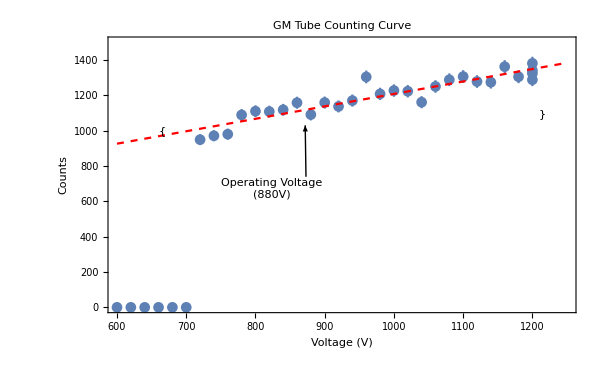

```mathematica
FPercentChangeInCountRatePer100V[c0_,c1_,v0_,v1_]:=(10^4*(c1-c0)/c0)/(v1-v0)
```

```mathematica
counts[[Length[counts]]]
Part1PercentChange=FPercentChangeInCountRatePer100V[counts[[7]],1333.5,voltage[[7]],1200]//N
```

1341

8.4409

```mathematica
eff[Subscript[x, 0]_]:=2 Subscript[x, 0]^2
D[eff[Subscript[x, 1]],Subscript[x, 1]]
```

4 x_1

```mathematica
D[FPercentChangeInCountRatePer100V[c0,c1,v0,v1],c0]
D[FPercentChangeInCountRatePer100V[c0,c1,v0,v1],c1]
```

-10000/(c0 (-v0+v1))-(10000 (-c0+c1))/(c0^2 (-v0+v1))

10000/(c0 (-v0+v1))

```mathematica
e0[c0_,c1_,v0_,v1_]=√((-10000/(c0 (-v0+v1))-(10000 (-c0+c1))/(c0^2 (-v0+v1)))^2*c0+(10000/(c0 (-v0+v1)))^2*c1)
```

√((100000000 c1)/(c0^2 (-v0+v1)^2)+c0 (-10000/(c0 (-v0+v1))-(10000 (-c0+c1))/(c0^2 (-v0+v1)))^2)

```mathematica
e0[949,1333.5,720,1200]//N
```

1.24326

The change in counts per 100V is 8.441±1.2 counts. The analysis would be similar for a calculation of count rate slope, since the count time for each point on the slope was the same (30s) and the error in the time was considered to be σ_t=0.

```mathematica
(* Choose 5 pairs of points from the dataset *)
RandomPointPairs=Table[RandomSample[PartAData[[7;;]],2],{i,5}]
(* Generate a list of slopes calculated from each of these pairs *)
SlopeArray=Table[(RandomPointPairs[[i,2,2]]-RandomPointPairs[[i,1,2]])/(RandomPointPairs[[i,2,1]]-RandomPointPairs[[i,1,1]]),{i,Length[RandomPointPairs]}]//N
PctChangeArray=SlopeArray/PartAData[[7,2]]*10^4
(* Calculate the average value and standard deviation of this slope array *)
Mean[PctChangeArray]
StandardDeviation[PctChangeArray]
(* Convert this slope to a percent change in counts per 100V *)
ComparibleValue=Mean[SlopeArray]/PartAData[[7,2]]*10^4;
```

{{{760,980,14 √5},{1040,1161,3 √129}},{{1160,1362,√1362},{1040,1161,3 √129}},{{920,1137,√1137},{1060,1250,25 √2}},{{920,1137,√1137},{740,971,√971}},{{1040,1161,3 √129},{720,949,√949}}}

{0.646429,1.675,0.807143,0.922222,0.6625}

{6.81168,17.6502,8.50519,9.71783,6.98103}

9.93318

4.47482

```mathematica
{{{980,1208,2 √302},{880,1091,√1091}},{{900,1159,√1159},{1080,1288,2 √322}},{{760,980,14 √5},{980,1208,2 √302}},{{1200,1381,√1381},{720,949,√949}},{{880,1091,√1091},{940,1170,3 √130}}}
```

{{{980,1208,2 √302},{880,1091,√1091}},{{900,1159,√1159},{1080,1288,2 √322}},{{760,980,14 √5},{980,1208,2 √302}},{{1200,1381,√1381},{720,949,√949}},{{880,1091,√1091},{940,1170,3 √130}}}

This value (9.933±4 %/100V is certainly within error of my calculated value above (8.441±1.2 %/100V). The large variance in my data drives a very high uncertainty.

Part B: Background

```mathematica
PartBBackgroundFile="tjacobi_lab3_RawBackground1.tsv";
PartBBackground=Import[NotebookDirectory[]<>PartBBackgroundFile];
BackgroundCountArray=Table[PartBBackground[[i,3]],{i,12,Length[PartBBackground]}]
```

{2,2,5,1,1,2,4,7,4,1,4,0,5,4,6,1,3,5,5,3,3,4,3,3,2,7,4,4,3,7,3,2,5,2,0,3,5,4,7,4,3,2,4,1,3,5,4,4,2,4,3,5,5,4,2,5,6,4,3,5,8,2,2,1,5,5,5,3,2,0,2,1,1,5,7,2,4,2,4,3,5,3,3,2,0,5,4,3,2,2,1,4,3,3,5,1,4,8,1,1,3,5,3,6,3,6,8,1,1,1,4,3,4,2,4,3,1,3,4,4,0,1,3,2,1,2,1,2,2,2,4,4,3,3,5,5,1,7,4,2,4,7,6,6,5,3,2,4,5,5,1,2,3,4,3,1,3,3,6,7,2,1,2,2,3,7,1,5,1,2,4,3,5,8,0,4,5,1,7,3,4,1,2,3,1,4,7,4,2,1,2,2,5,4,6,4,2,4,2,1,5,1,3,5,3,4,6,0,3,2,4,3,2,4,2,3,5,4,5,4,4,3,3,2,3,4,2,2,1,1,3,4,4,6,2,2,2,2,4,4,5,3,2,2,2,1,3,6,3,4,2,3,2,1,6,0,4,3,1,7,3,0,4,1,4,1,2,3,3,6,2,4,1,3,5,1,1,2,0,0,3,2,6,1,2,4,3,6,4,4,2,4,2,4,4,2,2,3,1,2}

```mathematica
(*Verify that we have 300 runs*)
Length[BackgroundCountArray]
```

300

```mathematica
TotalBackgroundCounts=Total[BackgroundCountArray]
```

961

1. Bin the collected data according to the number of counts measured

```mathematica
(* Define width of the bins for histogram *)
PartBBinWidth=1;
PartBDataBinned=BinCounts[BackgroundCountArray,PartBBinWidth]
(* Convert to 2-d array for plotting *)
PartBHistData=Multicolumn[Join[Table[i*PartBBinWidth,{i,-1,Length[PartBDataBinned]-1}],PartBDataBinned],2]//First
PartBNormedHistData=Multicolumn[Join[Table[i*PartBBinWidth,{i,-1,Length[PartBDataBinned]-1}],PartBDataBinned/Length[BackgroundCountArray]],2]//First
(* Mean of the measured distribution *)
PartBBackgroundMean=Mean[BackgroundCountArray]//N
```

{0,11,43,62,58,61,34,15,12,4}

{{-1,0},{0,11},{1,43},{2,62},{3,58},{4,61},{5,34},{6,15},{7,12},{8,4},{9,}}

{{-1,0},{0,11/300},{1,43/300},{2,31/150},{3,29/150},{4,61/300},{5,17/150},{6,1/20},{7,1/25},{8,1/75},{9,}}

3.20333

2. With this data, make a frequency (histogram) plot of the data. On the same plot, include the expected Poisson histogram and Gaussian distribution curve for comparison purposes. Be sure to include a legend and appropriate curves (colored, thick/thin, dashed/solid, etc.) to differentiate between the three (i.e., data, Poisson, and Gaussian).

```mathematica
Histogram[BackgroundCountArray];
(* Generate the histogram plot *)
pbdp=ListPlot[PartBHistData,Joined->True, InterpolationOrder->0, FrameTicksStyle->Directive[Black,12],PlotStyle->Orange,PlotLabel->Style["Normalized Background\nCounts Distribution",Black,24],Filling->Axis,FillingStyle->{Lighter[Orange,0.8]},PlotRange->{{0,10},{0,70}},FrameLabel->{Style["Counts",Black,20],Style["Observed",Black,20]},Frame->True,ImageSize->Full];
(* Make the Poisson distribution *)
PartBPoisson[c_]:=Length[BackgroundCountArray]*PartBBackgroundMean^c/(c!)ⅇ^-PartBBackgroundMean;
pbpp=Plot[PartBPoisson[c],{c,0,10},PlotRange->Automatic,PlotStyle->{Dotted,Blue},ImageSize->Full];
(* Make the Gaussian distribution *)
g = 1/(√(2 σ^2 π))ⅇ^(-(x-PartBBackgroundMean)^2/(2 σ^2));
PartBGaussFit=FindFit[PartBDataBinned/Length[BackgroundCountArray],g,{σ},x];
PartBGaussFunction[x_,sig_]=Length[BackgroundCountArray]/(√(2 sig^2 π))ⅇ^(-(x-PartBBackgroundMean)^2/(2 sig^2));
pbgp=Plot[PartBGaussFunction[c,PartBGaussFit[[1,2]]],{c,0,10},PlotRange->Automatic,PlotStyle->{Dashed,Red}];
(* Combine the plots *)
```

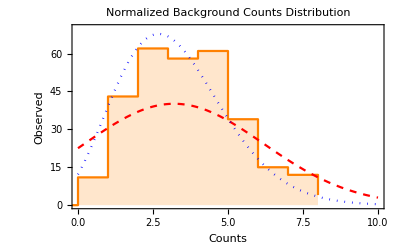

```mathematica
Show[pbdp,pbgp,pbpp]
```

Part C: Dead Time

```mathematica
PartCBlankBlank1={41,36,41};
PartCBlankSource={20925,20696,20843};
PartCSourceSource={35529,35636,35634};
PartCSourceBlank={20269,20216,20227};
PartCBlankBlank2={27,47,39};
```

Using equation 5 provided, determine the dead time for each of the three runs (i.e. each experiment was conducted three times, and we will analyze the data by finding the dead time three times. The first time will be using the data collected in the first 60 second run in the four data points collected, the second the second 60 second run, and the third the third 60 second run).

```mathematica
tau[m1_,m2_,m12_,mb_]=(2 m1 m2-√((2 m1 m2-2 m12 mb)^2-4 (m12+mb-m1-m2)*(m1 m12 mb+m2 m12 mb-m1 m2 mb-m1 m2 m12)))/(2 m1 m2 m12);
```

```mathematica
(* Calculate tau for each experiment *)
PartCDeadTimes=Table[tau[PartCBlankSource[[i]],PartCSourceBlank[[i]],PartCSourceSource[[i]],PartCBlankBlank1[[i]]],{i,1,3}]//N
```

{7.78424×10^-6,7.27543×10^-6,7.472×10^-6}

In a new cell with text input, comment on how well the three results agree with each other.

```mathematica
StandardDeviation[PartCDeadTimes]
Abs[(PartCDeadTimes-Mean[PartCDeadTimes])]/Mean[PartCDeadTimes]
```

2.56589×10^-7

{0.03644,0.0313064,0.00513358}

The standard deviation is on order of hundreds of nanoseconds, and each of these values is within 3-6% agreement with the mean. This is good agreement.

Now average them together and place the value and the GM tube number on the back cover of your laboratory notebook for future reference.

Now add m1 and m2 together and see if it adds up to the true count rate for m12 in the three experiments. Comment on whether the two values agree and why in an appropriate cell.

```mathematica
PartCSourceBlank+PartCBlankSource
```

{41194,40912,41070}

```mathematica
PartCSourceSource
```

{35529,35636,35634}

```mathematica
((PartCSourceBlank+PartCBlankSource)-PartCSourceSource)/(PartCSourceBlank+PartCBlankSource)//N
```

{0.13752,0.12896,0.132359}

These values do not agree closely--the sum of the two half-sources is higher. This is due to the dead time the detector experiences with higher activities--it misses some decay events.

Symbolically solve for the dead time starting from equation 2 and ending in equation 4. You may use Mathematica to check your answer, but the solution must be pen and paper. Scan this in and include it when turning in your completed assignment to the GTA.

Plot the measured count rate as a function of true count rate (y on x) and include a dead time-less detector line as well. Be sure to plot out far enough so that a clear separation between true count rate and measured count rate can be seen.

{48460.3,48659.5,48655.8}

{{48460.3,35529,√35529},{48659.5,35636,2 √8909},{48655.8,35634,√35634}}

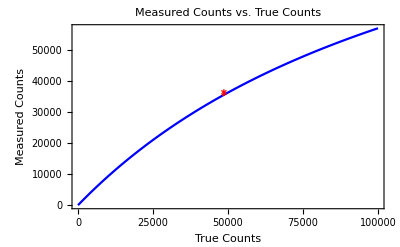

```mathematica
t=Mean[PartCDeadTimes];
m[n_]=n/(1+n*t);
n[m_]=m/(1-m*t);
PartCCurve=Plot[m[n],{n,0,100000}, AxesOrigin->{0,0},FrameLabel->{Style["True Counts",18],Style["Measured Counts",18]},Frame->True,PlotLabel->Style["Measured Counts vs.\nTrue Counts",24],FrameTicksStyle->Directive[Black,10],ImageSize->Full,PlotLegends->Placed[{"Calculated"},{0.15,0.85}],PlotStyle->Blue];
PartCTrueCounts=n[PartCSourceSource]
PartCDataPairs=Multicolumn[Join[PartCTrueCounts,PartCSourceSource,√PartCSourceSource],3]//First
PartCDataPlot=ErrorListPlot[PartCDataPairs,PlotMarkers->{"*",12},PlotStyle->Red,PlotLegends->Placed[{"Observed"},{0.15,0.85}]];
Show[PartCCurve,PartCDataPlot]
```

Part D: Counting Radiation Sources

```mathematica
PartDBackgroundFile="tjacobi_lab3_RawBackground2.tsv";
PartDCs137File="tjacobi_lab3_Cs137.tsv";
PartDCo60File="tjacobi_lab3_Co60x2.tsv";
```

```mathematica
PartDBackground=Import[NotebookDirectory[]<>PartDBackgroundFile][[12;;]][[;;,3]];
PartDCs137=Import[NotebookDirectory[]<>PartDCs137File][[12;;]][[;;,3]];
PartDCo60=Import[NotebookDirectory[]<>PartDCo60File][[12;;]][[;;,3]];
```

```mathematica
PartDBackground2={{"Description",""},{"Number of Runs",40},{"Preset Time",10},{"Pause Time",0},{"Alarm Level",0},{"High Voltage",880},{"Step Voltage",0},{"Volume",0},{""},{"Run","High","","Elapsed"},{"Number","Voltage","Counts","Time","Date/Time"},{1,880,8,10,"02/02/17 07:16:17 PM",""},{2,880,5,10,"02/02/17 07:16:27 PM",""},{3,880,5,10,"02/02/17 07:16:37 PM",""},{4,880,8,10,"02/02/17 07:16:47 PM",""},{5,880,9,10,"02/02/17 07:16:58 PM",""},{6,880,7,10,"02/02/17 07:17:08 PM",""},{7,880,2,10,"02/02/17 07:17:18 PM",""},{8,880,11,10,"02/02/17 07:17:28 PM",""},{9,880,2,10,"02/02/17 07:17:38 PM",""},{10,880,6,10,"02/02/17 07:17:48 PM",""},{11,880,5,10,"02/02/17 07:17:59 PM",""},{12,880,6,10,"02/02/17 07:18:09 PM",""},{13,880,10,10,"02/02/17 07:18:19 PM",""},{14,880,7,10,"02/02/17 07:18:29 PM",""},{15,880,3,10,"02/02/17 07:18:40 PM",""},{16,880,4,10,"02/02/17 07:18:50 PM",""},{17,880,10,10,"02/02/17 07:19:00 PM",""},{18,880,4,10,"02/02/17 07:19:10 PM",""},{19,880,5,10,"02/02/17 07:19:20 PM",""},{20,880,9,10,"02/02/17 07:19:31 PM",""},{21,880,8,10,"02/02/17 07:19:41 PM",""},{22,880,5,10,"02/02/17 07:19:51 PM",""},{23,880,4,10,"02/02/17 07:20:01 PM",""},{24,880,6,10,"02/02/17 07:20:12 PM",""},{25,880,9,10,"02/02/17 07:20:22 PM",""},{26,880,9,10,"02/02/17 07:20:32 PM",""},{27,880,7,10,"02/02/17 07:20:42 PM",""},{28,880,7,10,"02/02/17 07:20:53 PM",""},{29,880,12,10,"02/02/17 07:21:03 PM",""},{30,880,7,10,"02/02/17 07:21:13 PM",""},{31,880,8,10,"02/02/17 07:21:23 PM",""},{32,880,4,10,"02/02/17 07:21:33 PM",""},{33,880,5,10,"02/02/17 07:21:43 PM",""},{34,880,5,10,"02/02/17 07:21:54 PM",""},{35,880,6,10,"02/02/17 07:22:04 PM",""},{36,880,1,10,"02/02/17 07:22:14 PM",""},{37,880,7,10,"02/02/17 07:22:24 PM",""},{38,880,3,10,"02/02/17 07:22:34 PM",""},{39,880,5,10,"02/02/17 07:22:45 PM",""},{40,880,7,10,"02/02/17 07:22:55 PM",""}};
```

```mathematica
PartDCs137Two={{"Description",""},{"Number of Runs",40},{"Preset Time",10},{"Pause Time",0},{"Alarm Level",0},{"High Voltage",880},{"Step Voltage",0},{"Volume",0},{""},{"Run","High","","Elapsed"},{"Number","Voltage","Counts","Time","Date/Time"},{1,880,76,10,"02/02/17 07:25:04 PM",""},{2,880,94,10,"02/02/17 07:25:14 PM",""},{3,880,81,10,"02/02/17 07:25:25 PM",""},{4,880,84,10,"02/02/17 07:25:35 PM",""},{5,880,95,10,"02/02/17 07:25:45 PM",""},{6,880,110,10,"02/02/17 07:25:55 PM",""},{7,880,91,10,"02/02/17 07:26:06 PM",""},{8,880,120,10,"02/02/17 07:26:16 PM",""},{9,880,95,10,"02/02/17 07:26:26 PM",""},{10,880,87,10,"02/02/17 07:26:36 PM",""},{11,880,83,10,"02/02/17 07:26:47 PM",""},{12,880,92,10,"02/02/17 07:26:57 PM",""},{13,880,89,10,"02/02/17 07:27:07 PM",""},{14,880,91,10,"02/02/17 07:27:17 PM",""},{15,880,99,10,"02/02/17 07:27:27 PM",""},{16,880,116,10,"02/02/17 07:27:38 PM",""},{17,880,86,10,"02/02/17 07:27:48 PM",""},{18,880,92,10,"02/02/17 07:27:58 PM",""},{19,880,89,10,"02/02/17 07:28:09 PM",""},{20,880,109,10,"02/02/17 07:28:19 PM",""},{21,880,85,10,"02/02/17 07:28:29 PM",""},{22,880,108,10,"02/02/17 07:28:39 PM",""},{23,880,88,10,"02/02/17 07:28:49 PM",""},{24,880,80,10,"02/02/17 07:29:00 PM",""},{25,880,90,10,"02/02/17 07:29:10 PM",""},{26,880,88,10,"02/02/17 07:29:20 PM",""},{27,880,117,10,"02/02/17 07:29:30 PM",""},{28,880,92,10,"02/02/17 07:29:40 PM",""},{29,880,111,10,"02/02/17 07:29:51 PM",""},{30,880,87,10,"02/02/17 07:30:01 PM",""},{31,880,93,10,"02/02/17 07:30:11 PM",""},{32,880,100,10,"02/02/17 07:30:21 PM",""},{33,880,90,10,"02/02/17 07:30:32 PM",""},{34,880,92,10,"02/02/17 07:30:42 PM",""},{35,880,92,10,"02/02/17 07:30:52 PM",""},{36,880,96,10,"02/02/17 07:31:02 PM",""},{37,880,98,10,"02/02/17 07:31:12 PM",""},{38,880,97,10,"02/02/17 07:31:23 PM",""},{39,880,96,10,"02/02/17 07:31:33 PM",""},{40,880,88,10,"02/02/17 07:31:43 PM",""}};
```

```mathematica
PartDCo60x2Two={{"Description",""},{"Number of Runs",40},{"Preset Time",10},{"Pause Time",0},{"Alarm Level",0},{"High Voltage",880},{"Step Voltage",0},{"Volume",0},{""},{"Run","High","","Elapsed"},{"Number","Voltage","Counts","Time","Date/Time"},{1,880,44,10,"02/02/17 07:35:19 PM",""},{2,880,39,10,"02/02/17 07:35:29 PM",""},{3,880,26,10,"02/02/17 07:35:39 PM",""},{4,880,50,10,"02/02/17 07:35:50 PM",""},{5,880,42,10,"02/02/17 07:36:00 PM",""},{6,880,45,10,"02/02/17 07:36:10 PM",""},{7,880,29,10,"02/02/17 07:36:20 PM",""},{8,880,36,10,"02/02/17 07:36:31 PM",""},{9,880,31,10,"02/02/17 07:36:41 PM",""},{10,880,39,10,"02/02/17 07:36:51 PM",""},{11,880,34,10,"02/02/17 07:37:01 PM",""},{12,880,39,10,"02/02/17 07:37:12 PM",""},{13,880,27,10,"02/02/17 07:37:22 PM",""},{14,880,45,10,"02/02/17 07:37:32 PM",""},{15,880,44,10,"02/02/17 07:37:42 PM",""},{16,880,42,10,"02/02/17 07:37:53 PM",""},{17,880,47,10,"02/02/17 07:38:03 PM",""},{18,880,37,10,"02/02/17 07:38:13 PM",""},{19,880,35,10,"02/02/17 07:38:23 PM",""},{20,880,44,10,"02/02/17 07:38:34 PM",""},{21,880,53,10,"02/02/17 07:38:44 PM",""},{22,880,32,10,"02/02/17 07:38:54 PM",""},{23,880,41,10,"02/02/17 07:39:04 PM",""},{24,880,36,10,"02/02/17 07:39:15 PM",""},{25,880,39,10,"02/02/17 07:39:25 PM",""},{26,880,43,10,"02/02/17 07:39:35 PM",""},{27,880,39,10,"02/02/17 07:39:45 PM",""},{28,880,47,10,"02/02/17 07:39:56 PM",""},{29,880,30,10,"02/02/17 07:40:06 PM",""},{30,880,39,10,"02/02/17 07:40:16 PM",""},{31,880,45,10,"02/02/17 07:40:26 PM",""},{32,880,36,10,"02/02/17 07:40:36 PM",""},{33,880,41,10,"02/02/17 07:40:47 PM",""},{34,880,49,10,"02/02/17 07:40:57 PM",""},{35,880,33,10,"02/02/17 07:41:07 PM",""},{36,880,42,10,"02/02/17 07:41:17 PM",""},{37,880,37,10,"02/02/17 07:41:27 PM",""},{38,880,49,10,"02/02/17 07:41:38 PM",""},{39,880,41,10,"02/02/17 07:41:48 PM",""},{40,880,48,10,"02/02/17 07:41:58 PM",""}};
```

With the data collected, determine the average count rate, background corrected average count rate, and the uncertainty in each of the two runs (Cs-137 and Co-60).

```mathematica
PartDBackgroundAverage=Mean[PartDBackground]//N
```

6.275

```mathematica
PartDBackgroundUncertainty=StandardDeviation[PartDBackground]//N
```

2.52157

```mathematica
PartDCo60Average=Mean[PartDCo60]//N
```

39.875

```mathematica
PartDCo60Uncertainty=StandardDeviation[PartDCo60]//N
```

6.50912

```mathematica
PartDCo60BackgroundCorrectedAverage=PartDCo60Average-PartDBackgroundAverage//N
```

33.6

```mathematica
PartDCo60BackgroundCorrectedUncertainty=StandardDeviation[PartDCo60-PartDBackground]//N
```

6.72843

```mathematica
PartDCs137Average=Mean[PartDCs137]//N
```

94.175

```mathematica
PartDCs137Uncertainty=StandardDeviation[PartDCs137]//N
```

10.2929

```mathematica
PartDCs137BackgroundCorrectedAverage=PartDCs137Average-PartDBackgroundAverage//N
```

87.9

```mathematica
PartDCs137BackgroundCorrectedUncertainty=StandardDeviation[PartDCs137-PartDBackground]//N
```

10.3572

Why are the two average count rates different from each other? Answer in the Mathematica notebook.

These are different sources that have different activities. Therefore they should not be expected to be the same.

If the background uncertainty is ignored in the calculation, does this affect the calculated uncertainty? Clearly explain why or why not.

When including the background uncertainty, the combined error is √(σ_m^2+σ_b^2); without this the error is √(σ_m^2). Since in this case the background uncertainty is of comparable order of magnitude to the error in the measured signal, not including this error would have a significant effect on the results.